["Love"](https://www.dropbox.com/scl/fi/0e1dvmaq7ntwzenmu2n3a/Love-A.E.H.-A-Treatise-on-the-Mathematical-Theory-of-Elasticity-Dover-1944.pdf?dl=0&oref=e&r=ABBcNaMT95A1uEX9xQIgyO3MVOHySs_CuuW_JKkGB-EZ270Pdjo_7iH2trDfymp6Wv_QDRcO01mylLBC6cOQk-u_mLBixSAGcbMuFNARrjaXf3SxXuB3_gksgGpTdTgLJszcR_nur5WNgikfqaWEtqG52kzHYbzOU4Z5e8a6WdIgGNoL8sZsTXwjcCdANIn-BId_tU6qPCB_jP-kwt745I6z#comment_id=pid_comments:AAAAAHJ4bXEQfTokwI1W83MZx3cG_qexVY1gKQHIVcuNzBVY)

```mathematica
(*Off[Unset::norep];
Names@{"Global`*","SphereRotation`*", "SphereTranslation`*"};
ClearAll[#] & /@(%);
Remove[#] &/@(%%);*)
```

This is some text

MateX["x^2"]

## Notation

```mathematica
<<Notation`
Off[Remove::rmnsm];
RemoveSymbolize[Subscript[x_, 1]]
RemoveSymbolize[Subscript[x_, 2]]
RemoveSymbolize[Subscript[x_, 3]]
RemoveSymbolize[Subscript[x_, R]]
RemoveSymbolize[Subscript[x_, ϕ]]
RemoveSymbolize[Subscript[x_, θ]]



RemoveNotation[x__(i_·)   ⟺  x_[[i_]]]
RemoveNotation[x__(i_ ·j_·)   ⟺  x_[[i_,j_]]]
RemoveNotation[x__(i_ ·j_·k_·)   ⟺  x_[[i_,j_,k_]]]
RemoveNotation[x__(i_ ·j_·k_·l_·)   ⟺  x_[[i_,j_,k_,l_]]]


RemoveNotation[(x_)^-1   ⟺  Inverse[x_]]
RemoveNotation[A_⊙B_   ⟺  Sum[A_[[i,j]]B_[[i,j]],{i,1,3},{j,1,3}]]
RemoveNotation[A_ᵀ   ⟺  Transpose[A_]]
RemoveNotation[x__(i_·)   ⟺  x_[[i_]]]
RemoveNotation[x__(i_ ·j_·)   ⟺  x_[[i_,j_]]]
RemoveNotation[x__(i_ ·j_·k_·)   ⟺  x_[[i_,j_,k_]]]
RemoveNotation[x__(i_ ·j_·k_·l_·)   ⟺  x_[[i_,j_,k_,l_]]]






Symbolize[Subscript[x_, 1]]
Symbolize[Subscript[x_, 2]]
Symbolize[Subscript[x_, 3]]
Symbolize[Subscript[x_, R]]
Symbolize[Subscript[x_, ϕ]]
Symbolize[Subscript[x_, θ]]



Notation[x__(i_·)   ⟺  x_[[i_]]]
Notation[x__(i_ ·j_·)   ⟺  x_[[i_,j_]]]
Notation[x__(i_ ·j_·k_·)   ⟺  x_[[i_,j_,k_]]]
Notation[x__(i_ ·j_·k_·l_·)   ⟺  x_[[i_,j_,k_,l_]]]


Notation[(x_)^-1   ⟺  Inverse[x_]]
Notation[A_⊙B_   ⟺  Sum[A_[[i,j]]B_[[i,j]],{i,1,3},{j,1,3}]]
Notation[A_ᵀ   ⟺  Transpose[A_]]
Notation[x__(i_·)   ⟺  x_[[i_]]]
Notation[x__(i_ ·j_·)   ⟺  x_[[i_,j_]]]
Notation[x__(i_ ·j_·k_·)   ⟺  x_[[i_,j_,k_]]]
Notation[x__(i_ ·j_·k_·l_·)   ⟺  x_[[i_,j_,k_,l_]]]

<<HaneeshPackages`
Get[URLDownload["https://raw.githubusercontent.com/haneeshk/ForBetterMMAExperience/master/ToTerminal.wl"]]
```

```mathematica
If[ValueQ[SphereTranslation`sympaltte],NotebookClose[SphereTranslation`sympaltte]]
Quiet[Remove[#] ]& /@ {"SphereTranslation`*"};
Begin["SphereTranslation`"];
If[ValueQ[sympaltte],NotebookClose[sympaltte]]
Quiet[ClearAll[#] ]& /@ {"SphereTranslation`*"};
Get[URLDownload["https://raw.githubusercontent.com/haneeshk/ForBetterMMAExperience/master/ComplexSymbols.wl"]];
syms=AssignLabels[{"e_1","e_2","e_3","u","∇u","u","∇u","ϵ","σ","H","ϵ","σ","λ","μ","I","n_sd","^1u","^2u","^3u","^1u","^2u","^3u"}];
sympaltte=SymbolPalette["syms",syms,1];
"n_sd"=3;
"I"=Table[KroneckerDelta[i,j],{i,1,"n_sd"},{j,1,"n_sd"}];

Begin["`AI`"];
Hello=3;
End[];
End[];
AppendTo[$ContextPath, "SphereTranslation`"];
$ContextPath=DeleteDuplicates[$ContextPath]
```

Complex Symbols Package Loaded

{ComplexSymbols`,TerminalFuncs`,HaneeshPackages`,Notation`,MaTeX`,XMPTools`,PresenterTools`,PresenterTools`Styles`,DocumentationSearch`,ResourceLocator`,URLUtilities`,PacletManager`,System`,Global`,SphereTranslation`}

```mathematica
SphereTranslation`AI`Hello
```

3

```mathematica
Format[a[i_,j_]]:=Subscript[a,ToString[i]~~ToString[j]];
A=Table[a[i,j],{i,1,3},{j,1,3}];
A//MatrixForm
Aᵀ//MatrixForm
```

(a_11 | a_12 | a_13
a_21 | a_22 | a_23
a_31 | a_32 | a_33)

(a_11 | a_21 | a_31
a_12 | a_22 | a_32
a_13 | a_23 | a_33)

```mathematica
Subscript[V, 1][x_,y_,z_]=𝒸''[τ] z
```

z 𝒸''[τ]

```mathematica
Subscript[V, 1][a,b,c]
```

c 𝒸''[τ]

```mathematica
Block[{n=1},
({Subscript[u, 1][x_,y_,z_],Subscript[u, 2][x_,y_,z_],Subscript[u, 3][x_,y_,z_]}=-ρ/((λ+2μ)2(2n+3))Grad[(x^2+y^2+z^2)Subscript[V, 1][x,y,z],{x,y,z}] 
(*eq. 17 at ["Love"](https://www.dropbox.com/scl/fi/0e1dvmaq7ntwzenmu2n3a/Love-A.E.H.-A-Treatise-on-the-Mathematical-Theory-of-Elasticity-Dover-1944.pdf?dl=0&oref=e&r=ABBcNaMT95A1uEX9xQIgyO3MVOHySs_CuuW_JKkGB-EZ270Pdjo_7iH2trDfymp6Wv_QDRcO01mylLBC6cOQk-u_mLBixSAGcbMuFNARrjaXf3SxXuB3_gksgGpTdTgLJszcR_nur5WNgikfqaWEtqG52kzHYbzOU4Z5e8a6WdIgGNoL8sZsTXwjcCdANIn-BId_tU6qPCB_jP-kwt745I6z#comment_id=pid_comments:AAAAAHJ4bXEQfTokwI1W83MZx3cG_qexVY1gKQHIVcuNzBVY)*))]
```

{-(x z ρ 𝒸''[τ])/(5 (λ+2 μ)),-(y z ρ 𝒸''[τ])/(5 (λ+2 μ)),-(ρ (2 z^2 𝒸''[τ]+(x^2+y^2+z^2) 𝒸''[τ]))/(10 (λ+2 μ))}

```mathematica
ClearAll["u","ϵ","σ"]

"u"[Subscript[x, 1]:_,Subscript[x, 2]:_,Subscript[x, 3]:_]={Subscript[u, 1][Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],Subscript[u, 2][Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],Subscript[u, 3][Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]]}
"ϵ"["u":_,𝓍_,𝓎_,𝓏_]:=1/2((∇_{𝓍,𝓎,𝓏} "u"[𝓍,𝓎,𝓏]+(∇_{𝓍,𝓎,𝓏} "u"[𝓍,𝓎,𝓏])ᵀ));
"σ"["u":_,𝓍_,𝓎_,𝓏_]:=λ  "I" Tr["ϵ"["u",𝓍,𝓎,𝓏]]+2μ "ϵ"["u",𝓍,𝓎,𝓏]
```

{-(x_1 x_3 ρ 𝒸''[τ])/(5 (λ+2 μ)),-(x_2 x_3 ρ 𝒸''[τ])/(5 (λ+2 μ)),-(ρ (2 x_3^2 𝒸''[τ]+(x_1^2+x_2^2+x_3^2) 𝒸''[τ]))/(10 (λ+2 μ))}

```mathematica
"u"[a,b,c]
```

{-(a c ρ 𝒸''[τ])/(5 (λ+2 μ)),-(b c ρ 𝒸''[τ])/(5 (λ+2 μ)),-(ρ (2 c^2 𝒸''[τ]+(a^2+b^2+c^2) 𝒸''[τ]))/(10 (λ+2 μ))}

```mathematica
"ϵ"["u",Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]]//MatrixForm//ToTerminal
"σ"["u",Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]]//MatrixForm//ToTerminal
```

```mathematica
"σ"["u",Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]]//MatrixForm//ToTerminal
("σ"["u",Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]]-"σ"["u",Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]]ᵀ)//MatrixForm//ToTerminal
```

```mathematica
Div["σ"["u",Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}]+
+ρ Grad[Subscript[V, 1][Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}]
%//Simplify//ToTerminal
(*Divergence is satisfied*)
```

{0,0,ρ 𝒸''[τ]-(λ ρ 𝒸''[τ])/(λ+2 μ)-(2 μ ρ 𝒸''[τ])/(λ+2 μ)}

```mathematica
p[x,y,z]
```

p[x,y,z]

```mathematica
Block[{(*λ=1,μ=1,ℊ=1,ρ=1*)},
"σ"[p,Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]]//Simplify//MatrixForm//N
(*Div["σ"[p,Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}]//Simplify*)]
```

(0.5 ((3. λ+2. μ) {p^(1,0,0)[x_1,x_2,x_3],p^(0,1,0)[x_1,x_2,x_3],p^(0,0,1)[x_1,x_2,x_3]}ᵀ  +λ p^(0,0,1)[x_1,x_2,x_3]+λ p^(0,1,0)[x_1,x_2,x_3]+λ p^(1,0,0)[x_1,x_2,x_3]+2. μ p^(1,0,0)[x_1,x_2,x_3]) | μ ({p^(1,0,0)[x_1,x_2,x_3],p^(0,1,0)[x_1,x_2,x_3],p^(0,0,1)[x_1,x_2,x_3]}ᵀ  +p^(1,0,0)[x_1,x_2,x_3]) | μ ({p^(1,0,0)[x_1,x_2,x_3],p^(0,1,0)[x_1,x_2,x_3],p^(0,0,1)[x_1,x_2,x_3]}ᵀ  +p^(1,0,0)[x_1,x_2,x_3])
μ ({p^(1,0,0)[x_1,x_2,x_3],p^(0,1,0)[x_1,x_2,x_3],p^(0,0,1)[x_1,x_2,x_3]}ᵀ  +p^(0,1,0)[x_1,x_2,x_3]) | 0.5 ((3. λ+2. μ) {p^(1,0,0)[x_1,x_2,x_3],p^(0,1,0)[x_1,x_2,x_3],p^(0,0,1)[x_1,x_2,x_3]}ᵀ  +λ p^(0,0,1)[x_1,x_2,x_3]+λ p^(0,1,0)[x_1,x_2,x_3]+2. μ p^(0,1,0)[x_1,x_2,x_3]+λ p^(1,0,0)[x_1,x_2,x_3]) | μ ({p^(1,0,0)[x_1,x_2,x_3],p^(0,1,0)[x_1,x_2,x_3],p^(0,0,1)[x_1,x_2,x_3]}ᵀ  +p^(0,1,0)[x_1,x_2,x_3])
μ ({p^(1,0,0)[x_1,x_2,x_3],p^(0,1,0)[x_1,x_2,x_3],p^(0,0,1)[x_1,x_2,x_3]}ᵀ  +p^(0,0,1)[x_1,x_2,x_3]) | μ ({p^(1,0,0)[x_1,x_2,x_3],p^(0,1,0)[x_1,x_2,x_3],p^(0,0,1)[x_1,x_2,x_3]}ᵀ  +p^(0,0,1)[x_1,x_2,x_3]) | 0.5 ((3. λ+2. μ) {p^(1,0,0)[x_1,x_2,x_3],p^(0,1,0)[x_1,x_2,x_3],p^(0,0,1)[x_1,x_2,x_3]}ᵀ  +(λ+2. μ) p^(0,0,1)[x_1,x_2,x_3]+λ (p^(0,1,0)[x_1,x_2,x_3]+p^(1,0,0)[x_1,x_2,x_3])))

```mathematica
"σ"[p,x,y,z]//Eigenvalues
```

{1/2 λ (3 {p^(1,0,0)[x,y,z],p^(0,1,0)[x,y,z],p^(0,0,1)[x,y,z]}ᵀ  +p^(0,0,1)[x,y,z]+p^(0,1,0)[x,y,z]+p^(1,0,0)[x,y,z]),1/2 λ (3 {p^(1,0,0)[x,y,z],p^(0,1,0)[x,y,z],p^(0,0,1)[x,y,z]}ᵀ  +p^(0,0,1)[x,y,z]+p^(0,1,0)[x,y,z]+p^(1,0,0)[x,y,z]),1/2 (λ+2 μ) (3 {p^(1,0,0)[x,y,z],p^(0,1,0)[x,y,z],p^(0,0,1)[x,y,z]}ᵀ  +p^(0,0,1)[x,y,z]+p^(0,1,0)[x,y,z]+p^(1,0,0)[x,y,z])}

```mathematica
Subscript[e, 1]={1,0,0};
Subscript[e, 2]={0,1,0};
Subscript[e, 3]={0,0,1};
Subscript[g, 1]=Subscript[e, 3];
Subscript[Q, 1]=RotationMatrix[θ,Subscript[g, 1]];
Subscript[g, 2]=Subscript[Q, 1].Subscript[e, 2];
Subscript[Q, 2]=RotationMatrix[ϕ,Subscript[g, 2]];
Q=Subscript[Q, 2].Subscript[Q, 1];
%//.Conjugate[x_]->x;
%//.Abs[x_]->x;
Set[Q,%//Simplify];
(Subscript[e, R]=Subscript[f, 3]=Q.Subscript[e, 3]);
Echo[%//MatrixForm,"e_R ="];
(Subscript[e, ϕ]=Subscript[f, 1]=Q.Subscript[e, 1]);
Echo[%//MatrixForm,"e_ϕ ="];
(Subscript[e, θ]=Subscript[f, 2]=Q.Subscript[e, 2]);
Echo[%//MatrixForm,"e_θ ="];
(* from MathWorld*)
```

e_R = (Cos[θ] Sin[ϕ]
Sin[θ] Sin[ϕ]
Cos[ϕ])

e_ϕ = (Cos[θ] Cos[ϕ]
Cos[ϕ] Sin[θ]
-Sin[ϕ])

e_θ = (-Sin[θ]
Cos[θ]
0)

```mathematica
ClearAll[Subscript[u, R],Subscript[u, ϕ],Subscript[u, θ],"u"];
Block[{m=(2(λ+μ))/λ},

Subscript[u, R][R_,ϕ_,θ_]=(4 Subscript[C, 1](m-1))/m Cos[ϕ]/R;
Subscript[u, ϕ][R_,ϕ_,θ_]=-((3m -4)Subscript[C, 1])/m Sin[ϕ]/R;
Subscript[u, θ][R_,ϕ_,θ_]=0;
"u"[R_,ϕ_,θ_]={Subscript[u, R][R,ϕ,θ],Subscript[u, ϕ][R,ϕ,θ],Subscript[u, θ][R,ϕ,θ]};

p[x_,y_,z_]=(TransformedField["Spherical"->"Cartesian","u"[R,ϕ,θ], {R,ϕ,θ}->{x,y,z}]//FullSimplify)]
```

{(C_1 x z)/((x^2+y^2+z^2)^(3/2)),(C_1 y z)/((x^2+y^2+z^2)^(3/2)),(C_1 (2 z^2 (λ+2 μ)+x^2 (λ+3 μ)+y^2 (λ+3 μ)))/((x^2+y^2+z^2)^(3/2) (λ+μ))}

```mathematica
TransformedField["Cartesian"->"Spherical","σ"[p,x,y,z],{x,y,z}-> {R,ϕ,θ}]//FullSimplify
```

{{-(2 C_1 √(R^2) μ (3 λ+4 μ) Cos[ϕ])/(R^3 (λ+μ)),(2 C_1 √(R^2) μ^2 Sin[ϕ])/(R^3 (λ+μ)),0},{(2 C_1 √(R^2) μ^2 Sin[ϕ])/(R^3 (λ+μ)),(2 C_1 √(R^2) μ^2 Cos[ϕ])/(R^3 (λ+μ)),0},{0,0,(2 C_1 √(R^2) μ^2 Cos[ϕ])/(R^3 (λ+μ))}}

```mathematica
p[x,y,z]//Simplify
```

{(C_1 x z)/((x^2+y^2+z^2)^(3/2)),(C_1 y z)/((x^2+y^2+z^2)^(3/2)),(C_1 (2 z^2 (λ+2 μ)+x^2 (λ+3 μ)+y^2 (λ+3 μ)))/((x^2+y^2+z^2)^(3/2) (λ+μ))}

```mathematica
ClearAll["^1u","^2u","^3u","u"];
Block[{m=(2(λ+μ))/λ,Subscript[A, 1]=-(𝒸''[τ](λ+μ) ρ)/(10 (λ+2 μ) (λ+4 μ)),Subscript[B, 1]=(a^2 𝒸''[τ] ρ)/(2 (λ+4 μ))},
"^1u"[R_,ϕ_,θ_]=(TransformedField["Cartesian"->"Spherical","u"[x,y,z], {x,y,z}->{R,ϕ,θ}]//FullSimplify);
"^2u"[R_,ϕ_,θ_]={-2 Subscript[A, 1](m-4)/m R^2 Cos[ϕ],-2 Subscript[A, 1](3m-2)/m R^2 Sin[ϕ],0};
"^3u"[R_,ϕ_,θ_]={+Subscript[B, 1]Cos[ϕ],-Subscript[B, 1]Sin[ϕ],0};
"u"[R_,ϕ_,θ_]=("^1u"[R,ϕ,θ]+"^2u"[R,ϕ,θ]+"^3u"[R,ϕ,θ])//FullSimplify]
```

{((a-R) (a+R) ρ Cos[ϕ] 𝒸''[τ])/(2 (λ+4 μ)),((-a^2+R^2) ρ Sin[ϕ] 𝒸''[τ])/(2 (λ+4 μ)),0}

```mathematica
"u"[a,ϕ,θ]
```

{0,0,0}

```mathematica
p[x_,y_,z_]=(TransformedField["Spherical"->"Cartesian","u"[R,ϕ,θ], {R,ϕ,θ}->{x,y,z}]//FullSimplify)
```

{0,0,((a^2-x^2-y^2-z^2) ρ 𝒸''[τ])/(2 (λ+4 μ))}

```mathematica
Solve[(Subscript[B, 1]+a^2 (Subscript[A, 1] (-2+(4 λ)/(λ+μ))-(3 ℊ ρ)/(10 (λ+2 μ))))==0 && (-Subscript[B, 1]+a^2 (Subscript[A, 1] (-6+(2 λ)/(λ+μ))+(ℊ ρ)/(10 λ+20 μ)))==0,{Subscript[A, 1],Subscript[B, 1]}]
```

{{A_1→-(ℊ (λ+μ) ρ)/(10 (λ+2 μ) (λ+4 μ)),B_1→(a^2 ℊ ρ)/(2 (λ+4 μ))}}

```mathematica
("u"[R,ϕ,θ])//ToTerminal
WD`u[r_,θ_,ϕ_]={-(3 r^2 ρ Cos[θ])/(2 (3+2 n) (λ+2 μ)),(r^2 ρ Sin[θ])/(6 λ+4 n λ+12 μ+8 n μ),0} 
Block[{n=1,ℊ=1},
("u"[R,ϕ,θ]-WD`u[R,ϕ,θ])//Simplify]
(* From Weilin's calculation*)
```

{-(3 r^2 ρ Cos[θ])/(2 (3+2 n) (λ+2 μ)),(r^2 ρ Sin[θ])/(6 λ+4 n λ+12 μ+8 n μ),0}

{1/10 ρ Cos[ϕ] ((3 R^2)/(λ+2 μ)+(5 (a-R) (a+R) 𝒸''[τ])/(λ+4 μ)),1/2 ρ Sin[ϕ] (-R^2/(5 (λ+2 μ))+((-a^2+R^2) 𝒸''[τ])/(λ+4 μ)),0}

```mathematica
SetOptions[EvaluationNotebook[],WindowOpacity->1]
```

```mathematica
SetOptions[EvaluationNotebook[],BackgroundAppearance]
```

```mathematica
N
```

N

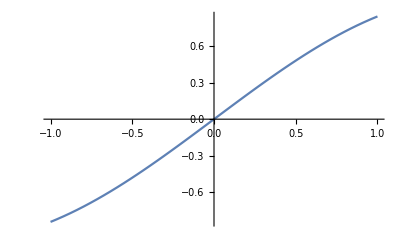

```mathematica
Plot[Sin[x],{x,-1,1}]
```

```mathematica
Div["σ"[p,Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]}]
```

{0,0,-(λ ρ 𝒸''[τ])/(λ+4 μ)-(4 μ ρ 𝒸''[τ])/(λ+4 μ)}

```mathematica
"I"={{1,0},{0,1}}
```

{{1,0},{0,1}}

```mathematica
"I"//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
Grad[f[ρ,ϕ,θ],{ρ,ϕ,θ},"Spherical"];
Div[%,{ρ,ϕ,θ},"Spherical"]//Simplify//pdConv
```

1/ρ^2(csc^2(ϕ) (∂^2 f(ρ,ϕ,θ))/(∂θ^2)+ρ^2 (∂^2 f(ρ,ϕ,θ))/(∂ρ^2)+(∂^2 f(ρ,ϕ,θ))/(∂ϕ^2)+2 ρ (∂f(ρ,ϕ,θ))/(∂ρ)+cot(ϕ) (∂f(ρ,ϕ,θ))/(∂ϕ))

```mathematica
TeXForm[({{-(R ℊ (λ+2 μ) ρ Cos[ϕ])/(λ+4 μ), (R ℊ μ ρ Sin[ϕ])/(λ+4 μ), 0}, {(R ℊ μ ρ Sin[ϕ])/(λ+4 μ), -(R ℊ λ ρ Cos[ϕ])/(λ+4 μ), 0}, {0, 0, -(R ℊ λ ρ Cos[ϕ])/(λ+4 μ)}})]
```

\left(
\begin{array}{ccc}
 -\frac{\rho  R \mathit{g}
   (\lambda +2 \mu ) \cos
   (\phi )}{\lambda +4 \mu } &
   \frac{\mu  \rho  R
   \mathit{g} \sin (\phi
   )}{\lambda +4 \mu } & 0 \\
 \frac{\mu  \rho  R \mathit{g}
   \sin (\phi )}{\lambda +4
   \mu } & -\frac{\lambda 
   \rho  R \mathit{g} \cos
   (\phi )}{\lambda +4 \mu } &
   0 \\
 0 & 0 & -\frac{\lambda  \rho 
   R \mathit{g} \cos (\phi
   )}{\lambda +4 \mu } \\
\end{array}
\right)

```mathematica
MaTeX[({{-(R ℊ (λ+2 μ) ρ Cos[ϕ])/(λ+4 μ), (R ℊ μ ρ Sin[ϕ])/(λ+4 μ), 0}, {(R ℊ μ ρ Sin[ϕ])/(λ+4 μ), -(R ℊ λ ρ Cos[ϕ])/(λ+4 μ), 0}, {0, 0, -(R ℊ λ ρ Cos[ϕ])/(λ+4 μ)}})]//MatrixForm
```

(-Graphics-
-Graphics-
-Graphics-)

```mathematica
?TeXForm
```

```mathematica
MaTeX[#,FontSize->28]&/@{{-(R (λ+2 μ) ρ Cos[ϕ] 𝒸''[τ])/(λ+4 μ),(R μ ρ Sin[ϕ] 𝒸''[τ])/(λ+4 μ),0},{(R μ ρ Sin[ϕ] 𝒸''[τ])/(λ+4 μ),-(R λ ρ Cos[ϕ] 𝒸''[τ])/(λ+4 μ),0},{0,0,-(R λ ρ Cos[ϕ] 𝒸''[τ])/(λ+4 μ)}}
%//MatrixForm
```

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

(-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-)

```mathematica
(*(∂ p)/(∂r)=ρ r ω^2*)

ClearAll[R,ρ,ω,p]
p[r_,ω_]=(ρ r^2 ω^2)/2
ρ=1000;

p[15.2 10^-2,50]

Quantity[p[15.2 10^-2,50],"Pascals"]
UnitConvert[Quantity[1,"Atmospheres"],"Kilopascals"]//N
%%/%
```

```mathematica
Quantity[p[15.2 10^-2,50],"Pascals"]/1000
```

28.88 Pa

```mathematica
p[15.2 10^-2,50]//FullForm
```

28880.

```mathematica
10
```

```mathematica
30000 revolution/minute

30000 (2π radian)/(60 seconds)

(30000 2π)/60 (radians/seconds)//N
```

3141.59

```mathematica
UnitConvert[Quantity[30000,"Revolutions"]/Quantity[1,"Minutes"],"Radians"]
```

Quantity::compat: Revolutions/Minutes and Radians are incompatible units

$Failed

0.588